## Constructing the Matrix Corresponding to the Derivative Operator, on the Hierarchical Basis

```mathematica
ϕ[x_]:=If[Abs[x]>1,0,1-Abs[x]]
ϕ[l_,i_]:=(ϕ[2^l(#-2^-l(2i-1))]&)
ceil[x_]:=1+Floor[x]
dϕ[x_]:=If[Abs[x]>1,0,
			If[x==1 ,-1/2,
			If[x==-1,1/2,
			If[x==0,0,
			If[x>0,-1,1]]]]](* Don't think I need this*)


test[x_]:=Sin[Pi x]^2
dtest[x_]:=2 Pi Cos[Pi x] Sin[Pi x]
```

```mathematica
getCoefficient[f_,x_,l_]:=f[x]-1/2 f[x+2^-l]-1/2 f[x-2^-l]
hierarchicalCoefficients[f_,l_]:={{f[1],f[0]}}~Append~Table[Table[getCoefficient[f,2^-k i,k],{i,1,2^k-1,2}],{k,1,l}]

Reconstruct[coefficients_]:=If[#==1,coefficients[[1,1]],
coefficients[[1,1]]#+coefficients[[1,2]](1-#)+Sum[coefficients[[2,l,ceil[2^(l-1)#]]] ϕ[2^l(#-2^-l(2ceil[2^(l-1)#]-1))],{l,1,Length[coefficients[[2]]]}]]&

project[f_,l_]:=Reconstruct[hierarchicalCoefficients[f,l]]
```

```mathematica
diff[f_,l_]:=If[#< 2^-l, diff[diff[f,l+1],l+1][2^-l]# (*(f[#+2^(-l-2)]-f[#])/2^(-l-2)*),If[#> 1-2^-l, diff[diff[f,l+1],l+1][1-2^-l](#-1),(f[#+2^-l]-f[#-2^-l])/(2 2^-l)]]&
diffNaive[f_,l_]:=If[#< 2^-l,(f[#+2^-l]-f[#])/2^-l,If[#> 1-2^-l,(f[#]-f[#-2^-l])/2^-l ,(f[#+2^-l]-f[#-2^-l])/(2 2^-l)]]&
diffFree[f_,l_]:=(f[#+2^-l]-f[#-2^-l])/(2 2^-l)&
```

```mathematica
hierarchicalCoefficients[diffFree[ϕ[2(#-1/2)]&,5],5]
```

{{-1,1},{{0},{3/2,-3/2},{1/2,1,-1,-1/2},{1/2,0,0,1,-1,0,0,-1/2},{1/2,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,-1/2}}}

```mathematica
{hierarchicalCoefficients[diff[ϕ[2(#-1/2)]&,5],5][[2]][[1;;3]]//Flatten,hierarchicalCoefficients[diff[ϕ[4(#-1/4)]&,5],5][[2]][[1;;3]]//Flatten,
hierarchicalCoefficients[diff[ϕ[4(#-3/4)]&,5],5][[2]][[1;;3]]//Flatten,
hierarchicalCoefficients[diff[ϕ[8(#-1/8)]&,5],5][[2]][[1;;3]]//Flatten,
hierarchicalCoefficients[diff[ϕ[8(#-3/8)]&,5],5][[2]][[1;;3]]//Flatten,
hierarchicalCoefficients[diff[ϕ[8(#-5/8)]&,5],5][[2]][[1;;3]]//Flatten,
hierarchicalCoefficients[diff[ϕ[8(#-7/8)]&,5],5][[2]][[1;;3]]//Flatten}
```

{{0,2,-2,1,1,-1,-1},{-2,1,1,4,-3,1,0},{2,-1,-1,0,-1,3,-4},{0,-4,0,2,2,0,0},{-4,6,2,-2,0,2,0},{4,-2,-6,0,-2,0,2},{0,0,4,0,0,-2,-2}}

```mathematica
PadRight[matrix[3],Automatic,0]
```

{{0,2,-2,1,1,-1,-1},{-2,1,1,4,-3,1,0},{2,-1,-1,0,-1,3,-4},{0,-4,0,2,2,0,0},{-4,6,2,-2,0,2,0},{4,-2,-6,0,-2,0,2},{0,0,4,0,0,-2,-2}}

```mathematica
Eigenvalues[{{0,2,-2,1,1,-1,-1},{-2,1,1,4,-3,1,0},{2,-1,-1,0,-1,3,-4},{0,-4,0,2,2,0,0},{-4,6,2,-2,0,2,0},{4,-2,-6,0,-2,0,2},{0,0,4,0,0,-2,-2}}]
```

{4 ⅈ √(2+√2),-4 ⅈ √(2+√2),4 ⅈ √2,-4 ⅈ √2,4 ⅈ √(2-√2),-4 ⅈ √(2-√2),0}

```mathematica
matrix[n_]:=Flatten[Table[Table[hierarchicalCoefficients[diff[ϕ[l,i],n],n][[2]]//Flatten,{i,1,2^(l-1)}],{l,1,n}],1]
```

```mathematica
matrix[3]
```

{{0,2,-2,1,1,-1,-1},{-2,1,1,4,-3,1,0},{2,-1,-1,0,-1,3,-4},{0,-4,0,2,2,0,0},{-4,6,2,-2,0,2,0},{4,-2,-6,0,-2,0,2},{0,0,4,0,0,-2,-2}}

```mathematica
PadRight[matrix[7],Automatic,0]//Transpose//Eigenvalues//N
```

{0.+127.961 ⅈ,0.-127.961 ⅈ,0.+127.846 ⅈ,0.-127.846 ⅈ,0.+127.653 ⅈ,0.-127.653 ⅈ,0.+127.384 ⅈ,0.-127.384 ⅈ,0.+127.037 ⅈ,0.-127.037 ⅈ,0.+126.615 ⅈ,0.-126.615 ⅈ,0.+126.116 ⅈ,0.-126.116 ⅈ,0.+125.541 ⅈ,0.-125.541 ⅈ,0.+124.89 ⅈ,0.-124.89 ⅈ,0.+124.164 ⅈ,0.-124.164 ⅈ,0.+123.363 ⅈ,0.-123.363 ⅈ,0.+122.488 ⅈ,0.-122.488 ⅈ,0.+121.54 ⅈ,0.-121.54 ⅈ,0.+120.518 ⅈ,0.-120.518 ⅈ,0.+119.423 ⅈ,0.-119.423 ⅈ,0.+118.257 ⅈ,0.-118.257 ⅈ,0.+117.019 ⅈ,0.-117.019 ⅈ,0.+115.711 ⅈ,0.-115.711 ⅈ,0.+114.333 ⅈ,0.-114.333 ⅈ,0.+112.886 ⅈ,0.-112.886 ⅈ,0.+111.371 ⅈ,0.-111.371 ⅈ,0.+109.789 ⅈ,0.-109.789 ⅈ,0.+108.141 ⅈ,0.-108.141 ⅈ,0.+106.428 ⅈ,0.-106.428 ⅈ,0.+104.651 ⅈ,0.-104.651 ⅈ,0.+102.811 ⅈ,0.-102.811 ⅈ,0.+100.908 ⅈ,0.-100.908 ⅈ,0.+98.9453 ⅈ,0.-98.9453 ⅈ,0.+96.9227 ⅈ,0.-96.9227 ⅈ,0.+94.8417 ⅈ,0.-94.8417 ⅈ,0.+92.7036 ⅈ,0.-92.7036 ⅈ,0.+90.5097 ⅈ,0.-90.5097 ⅈ,0.+88.2612 ⅈ,0.-88.2612 ⅈ,0.+85.9595 ⅈ,0.-85.9595 ⅈ,0.+83.6061 ⅈ,0.-83.6061 ⅈ,0.+81.2023 ⅈ,0.-81.2023 ⅈ,0.+78.7496 ⅈ,0.-78.7496 ⅈ,0.+76.2495 ⅈ,0.-76.2495 ⅈ,0.+73.7034 ⅈ,0.-73.7034 ⅈ,0.+71.113 ⅈ,0.-71.113 ⅈ,0.+68.4797 ⅈ,0.-68.4797 ⅈ,0.+65.8052 ⅈ,0.-65.8052 ⅈ,0.+63.091 ⅈ,0.-63.091 ⅈ,0.+60.3388 ⅈ,0.-60.3388 ⅈ,0.+57.5503 ⅈ,0.-57.5503 ⅈ,0.+54.7271 ⅈ,0.-54.7271 ⅈ,0.+51.8709 ⅈ,0.-51.8709 ⅈ,0.+48.9835 ⅈ,0.-48.9835 ⅈ,0.+46.0666 ⅈ,0.-46.0666 ⅈ,0.+43.1219 ⅈ,0.-43.1219 ⅈ,0.+40.1513 ⅈ,0.-40.1513 ⅈ,0.+37.1564 ⅈ,0.-37.1564 ⅈ,0.+34.1392 ⅈ,0.-34.1392 ⅈ,0.+31.1015 ⅈ,0.-31.1015 ⅈ,0.+28.045 ⅈ,0.-28.045 ⅈ,0.+24.9716 ⅈ,0.-24.9716 ⅈ,0.+21.8831 ⅈ,0.-21.8831 ⅈ,0.+18.7815 ⅈ,0.-18.7815 ⅈ,0.+15.6686 ⅈ,0.-15.6686 ⅈ,0.+12.5462 ⅈ,0.-12.5462 ⅈ,0.+9.41626 ⅈ,0.-9.41626 ⅈ,0.+6.28066 ⅈ,0.-6.28066 ⅈ,0.+3.14128 ⅈ,0.-3.14128 ⅈ,0.}

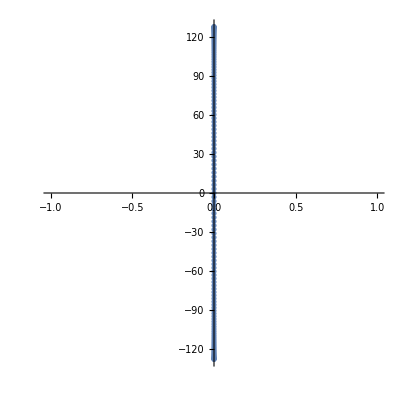

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@%366,AspectRatio->1]
```

Note the spectrum of the matrix representing d/dx is pretty much uniform, as is to be expected.